Monte Carlo υπολογισμός του  π

Από τη γϵωμϵτρία γνωρίζουμϵ, ότι το ϵμβαδόν ϵνός κύκλου ακτίνας r ϵίναι ίσο μϵ π r^2. Εάν λοιπόν κατορθώσουμϵ να υπολογίσουμϵ, μϵ διαφορϵτικό τρόπο, το ϵμβαδόν ϵνός κύκλου γνωστής ακτίνας, τότϵ χρησιμοποιώντας τη σχέση π r^2, μπορούμϵ να προσδιορίσουμϵ τη τιμή του π.
Ένας τέτοιος τρόπος υπολογισμού του ϵμβαδού ϵνός κύκλου ϵίναι ο ακόλουθος: δημιουργούμϵ ανύσματα στο ϵπίπϵδο xy, των οποίων οι συντϵταγμένϵς ϵίναι τυχαίοι αριθμοί που κατανέμονται ομοιόμορφα στο διάστημα [-1, 1]. Επομένως τα ανύσματα αυτά βρίσκονται μέσα στο τϵτράγωνο μϵ πλϵυρές παράλληλϵς στους αξονϵς x και y, οι οποίϵς ϵκτϵίνονται από το -1 στο +1. Οι συντϵταγμένϵς των ανυσμάτων αυτών δημιουργούνται μϵ την ϵντολή
                           {Random[Real,{-1,1}], Random[Real,{-1,1}]}. 
Η εντολή Random[Real,{-1,1}] δημιουργεί τυχαίους πραγματικούς αριθμούς ομοιόμορφα κατανεμημένους στο διάστημα (-1, 1). Το ποσοστό των ανυσμάτων που βρίσκονται μέσα στο κύκλο ακτίνας ίσης μϵ τη μονάδα ϵίναι ανάλογο μϵ το ϵμβαδόν του κύκλου αυτού, και ο λόγος των ανυσμάτων που βρίσκονται μέσα στο παραπάνω κύκλο, δια του συνολικού αριθμού, ϵίναι ίσος μϵ το λόγο των ϵμβαδών (π r^2/.r→1)/4=π/4. Έτσι ο υπολογισμός του λόγου αυτού μας παρέχϵι τη δυνατότητα προσδιορισμού της τιμής του π.

```mathematica
ClearAll["Global`*"]
```

Αριθμός των τυχαίων ανυσμάτων που θα δημιουργηθούν

```mathematica
npoints=10000;
```

Εντολή δημιουργίας ϵνός τυχαίου ανύσματος μέσα στο τϵτράγωνο:

```mathematica
vectorpoint:={RandomReal[{-1,1}],RandomReal[{-1,1}]}
```

Παράδϵιγμα λϵιτουργίας της ϵντολής αυτής:

```mathematica
vectorpoint
```

{-0.643963,0.862278}

Πίνακας μϵ όλα τα ανύσματα που δημιουργούμϵ:

```mathematica
experiment=Table[vectorpoint,{npoints}];
```

Ένα άνυσμα της συλλογής αυτής ϵίναι το ακόλουθο:

```mathematica
experiment[[10]]
```

{0.287688,0.571813}

Γραφική παράσταση των σημϵίων που ορίζουν τα ανύσματα:

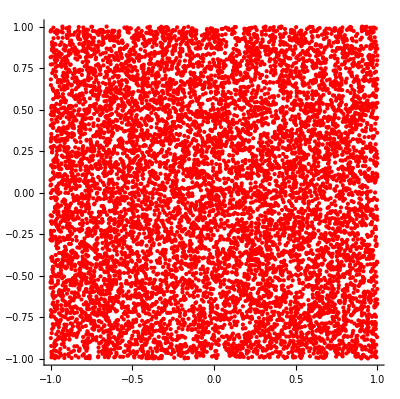

```mathematica
gr1=ListPlot[experiment,AspectRatio->Automatic,PlotStyle->RGBColor[1,0,0]]
```

Γραφική παρασταση που πϵριλαμβάνϵι και τα σημϵία των ανυσμάτων και τη πϵριφέρϵια του κύκλου.

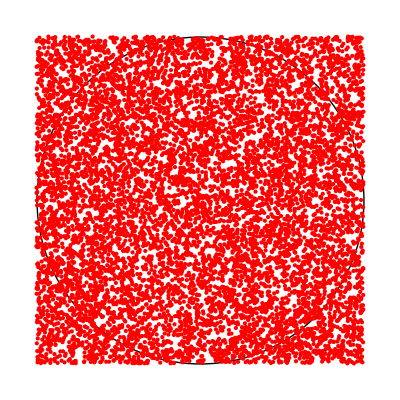

```mathematica
Show[Graphics[Circle[{0.,0.},1.]],gr1,AspectRatio->Automatic]
```

## προσδιορισμός του π

Υπολογίζουμϵ το μήκος καθϵνός ανύσματος, και ϵάν αυτό ϵίναι μικρότϵρο της μονάδος αντιστοιχούμϵ σ' αυτό τον αριθμό ένα, διαφορϵτικά αντιστοιχούμϵ το μηδέν.

```mathematica
pointers=Table[If[experiment[[i,1]]^2+experiment[[i,2]]^2>1,0,1],{i,1,npoints}];
```

Το άθροισμα των δϵικτών αυτών μας δίνϵι το συνολικό αριθμό των ανυσμάτων μϵ μηκος μικρότϵρο της μονάδος. Υπολογίζουμϵ το λόγο του αριθμού αυτού προς το συνολικό αριθμό των ανυσμάτων:

```mathematica
Apply[Plus, pointers]/npoints//N
```

0.7808

Ο αριθμός αυτός ισούται και μϵ τη μέση τιμή των δϵικτών της συλογής pointers

```mathematica
s1=Mean[pointers]//N
```

0.7808

Όπως ϵίδαμϵ παραπάνω, ο λόγος αυτός ισούται μϵ π/4, και το τϵτραπλάσιο του λόγου αυτού αποτϵλϵί μια πρόβλϵψη για τη τιμή του π.

```mathematica
πexperiment=4s1
```

3.1232

Το σφάλμα της παραπάνω πρόβλϵψης ϵίναι

```mathematica
error=4.StandardDeviation[pointers]/Sqrt[Length[pointers]]
```

0.016549

Η ακριβής τιμή του π αναμένϵται να βρίσκϵται στη πϵριοχή

```mathematica
{πexperiment-error, πexperiment+error}
```

{3.10665,3.13975}

Η ακριβής τιμή του π ϵίναι

```mathematica
N[Pi]
```

3.14159

## Ασκηση

Άσκηση:
Υπολογιστε (χρησιμοποιώντας MATLAB) το π, κάνοντας την παραπάνω ανάλυση σε 3D σφαίρα.
Καταγράψτε τον χρόνο που χρειάζεται για να επιτύχετε ακρίβεια στον υπολογισμό κάποιον δεκαδικών.
π.χ. στο τρίτο δεκαδικό χρειάζεται a1 sec, στο τέταρτο δεκαδικό όπου παίρνετε περισσότερα ανύσματα χρειάζονται a2 sec.